## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="ENO";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_trp.csv";

mainFolder = "fit_ENO_TEST_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName,  assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{2pg,Null,Keq substrate}

{5.19,Keq value}

{2pg,Km or S05 substrate}

{0.0001,Km or S05 value}

{{{2pg,Null}},kcat substrates}

{100,kcat value}

((2pg)^c⇌h2o^c+pep^c)^ENO

Null;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg,Null | 5.19 | 4.9305
5.4495 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | 0.0001 | 0.000095
0.000105 | mg2 | 0.001
so4 | 0.001 |  | 8.1 | 30 | trishcl | 0.05 | cl | 0.1
k | 0.1

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | Null | 100 | 95.
105. | 1/s | 8.1 | 30 | trishcl | 0.05 | cl | 0.1
k | 0.1

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities = Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((2pg)^c⇌h2o^c+pep^c)^ENO

Null;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg,Null | 5.19 | 4.9305
5.4495 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | 0.0001 | 0.000095
0.000105 | mg2 | 0.001
so4 | 0.001 |  | 8.1 | 30 | trishcl | 0.05 | cl | 0.1
k | 0.1

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | Null | 100 | 95.
105. | 1/s | 8.1 | 30 | trishcl | 0.05 | cl | 0.1
k | 0.1

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_ENO[c] + 2pg[c] <=> E_ENO[c]&2pg",
				"E_ENO[c]&2pg <=> E_ENO[c]&pep",
				"E_ENO[c]&pep <=> E_ENO[c] + pep[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((ENO^c)_^+(2pg)^c⇌(ENO^c&(2pg)^c)_^)^ENO1,((ENO^c&pep^c)_^⇌(ENO^c)_^+pep^c)^ENO2,((ENO^c&(2pg)^c)_^⇌(ENO^c&pep^c)_^)^ENO3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((ENO^c)_^+(2pg)^c⇌(ENO^c&(2pg)^c)_^)^ENO1,Overscript[(ENO^c&pep^c)_^⇌(ENO^c)_^+pep^c, ENO2],((ENO^c&(2pg)^c)_^⇌(ENO^c&pep^c)_^)^ENO3};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=2;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{(2pg)^c→0}

{pep^c→0}

{(2pg)^c→∞}

{pep^c→∞}

Added inhibition reactions:

{}

Generating flux equation...

{((ENO^c&(2pg)^c)_^-((ENO^c&pep^c)_^)/K_ENO3) Volume_c k_ENO3^⟶}

Volume_c (-(ENO^c&pep^c)_^ k_ENO3^⟵+(ENO^c&(2pg)^c)_^ k_ENO3^⟶)

1

2

3

0.03813

4

0.00022

5

0.000086

Simplifying...

6

0.02269

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={(*{1, (Subscript[k, GAPD1]^⟶Subscript[k, GAPD2]^⟶Subscript[k, GAPD3]^⟶Subscript[k, GAPD4]^⟶Subscript[k, GAPD5]^⟶)/(Subscript[k, GAPD1]^⟵Subscript[k, GAPD2]^⟵Subscript[k, GAPD3]^⟵Subscript[k, GAPD4]^⟵Subscript[k, GAPD5]^⟵), 4.25*10^2,{0.9*4.25*10^2,1.1*4.25*10^2}}*)};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	2pg[c]	pep[c]	param_ENO_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/haldaneRatio_1.txt"	5.19
1	0.00001	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/relRateFor_2pg.txt"	0.09090909090909091
1	0.00001584893192461114	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/relRateFor_2pg.txt"	0.13680688860321005
1	0.000025118864315095822	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/relRateFor_2pg.txt"	0.20076000891310186
1	0.000039810717055349695	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/relRateFor_2pg.txt"	0.2847472489508013
1	0.00006309573444801929	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/relRateFor_2pg.txt"	0.3868631798468568
1	0.0001	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/relRateFor_2pg.txt"	0.5
1	0.00015848931924611142	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/relRateFor_2pg.txt"	0.6131368201531432
1	0.0002511886431509582	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/relRateFor_2pg.txt"	0.7152527510491988
1	0.00039810717055349735	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/relRateFor_2pg.txt"	0.7992399910868982
1	0.000630957344480193	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/relRateFor_2pg.txt"	0.8631931113967899
1	0.001	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/relRateFor_2pg.txt"	0.9090909090909091
1	0.01	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/absRateFor.txt"	100
1	0.01	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/absRateFor.txt"	100
1	0.01	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/absRateFor.txt"	100
1	0.01	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/absRateFor.txt"	100
1	0.01	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/absRateFor.txt"	100
1	0.01	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/absRateFor.txt"	100
1	0.01	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/absRateFor.txt"	100
1	0.01	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/absRateFor.txt"	100
1	0.01	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/absRateFor.txt"	100
1	0.01	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/absRateFor.txt"	100
1	0.01	0	1	8.1	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/absRateFor.txt"	100

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
0.7	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
0.7	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
0.7	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
0.7	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
0.7	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
0.7	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
0.7	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
0.7	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
0.7	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
0.7	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
0.7	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/relRateFor_2pg.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/relRateRev_pep.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/relRateFor_2pg.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/relRateRev_pep.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_ENO_TEST_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 1.06767123063
best_fit: 0.723254018114
best_fit: 0.833434631315
best_fit: 0.313886790242
best_fit: 1.04017753999

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 1.54221×10^-12 | 2.37841×10^-24 | 1.84297×10^-11 | 3.551×10^-10 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.54221×10^-12 | 2.37841×10^-24 | 1.84297×10^-11 | 3.551×10^-10 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.54221×10^-12 | 2.37841×10^-24 | 1.84297×10^-11 | 3.551×10^-10 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.54221×10^-12 | 2.37841×10^-24 | 1.84297×10^-11 | 3.551×10^-10 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.54221×10^-12 | 2.37841×10^-24 | 1.84297×10^-11 | 3.551×10^-10 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.54221×10^-12 | 2.37841×10^-24 | 1.84297×10^-11 | 3.551×10^-10 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.54221×10^-12 | 2.37841×10^-24 | 1.84297×10^-11 | 3.551×10^-10 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.54221×10^-12 | 2.37841×10^-24 | 1.84297×10^-11 | 3.551×10^-10 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.54221×10^-12 | 2.37841×10^-24 | 1.84297×10^-11 | 3.551×10^-10 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.54221×10^-12 | 2.37841×10^-24 | 1.84297×10^-11 | 3.551×10^-10 | 5.19 | 5.19
1 | haldaneRatio_1 | 1.54221×10^-12 | 2.37841×10^-24 | 1.84297×10^-11 | 3.551×10^-10 | 5.19 | 5.19
1 | relRateFor_2pg | 8.88845×10^-13 | 7.90045×10^-25 | 1.86087×10^-13 | 2.04696×10^-10 | 0.0909091 | 0.0909091
1 | relRateFor_2pg | 8.44103×10^-13 | 7.12509×10^-25 | 2.65898×10^-13 | 1.9436×10^-10 | 0.136807 | 0.136807
1 | relRateFor_2pg | 7.81597×10^-13 | 6.10894×10^-25 | 3.61294×10^-13 | 1.79963×10^-10 | 0.20076 | 0.20076
1 | relRateFor_2pg | 6.99329×10^-13 | 4.89062×10^-25 | 4.58578×10^-13 | 1.61047×10^-10 | 0.284747 | 0.284747
1 | relRateFor_2pg | 5.99465×10^-13 | 3.59358×10^-25 | 5.34017×10^-13 | 1.38038×10^-10 | 0.386863 | 0.386863
1 | relRateFor_2pg | 4.88942×10^-13 | 2.39064×10^-25 | 5.62883×10^-13 | 1.12577×10^-10 | 0.5 | 0.5
1 | relRateFor_2pg | 3.78253×10^-13 | 1.43075×10^-25 | 5.34017×10^-13 | 8.70959×10^-11 | 0.613137 | 0.613137
1 | relRateFor_2pg | 2.78361×10^-13 | 7.74847×10^-26 | 4.58411×10^-13 | 6.40908×10^-11 | 0.715253 | 0.715253
1 | relRateFor_2pg | 1.96301×10^-13 | 3.85342×10^-26 | 3.61267×10^-13 | 4.52013×10^-11 | 0.79924 | 0.79924
1 | relRateFor_2pg | 1.33782×10^-13 | 1.78976×10^-26 | 2.65898×10^-13 | 3.0804×10^-11 | 0.863193 | 0.863193
1 | relRateFor_2pg | 8.89427×10^-14 | 7.91081×10^-27 | 1.86184×10^-13 | 2.04803×10^-11 | 0.909091 | 0.909091
1 | absRateFor | 1.26876×10^-12 | 1.60976×10^-24 | 2.92118×10^-10 | 2.92118×10^-10 | 100 | 100.
1 | absRateFor | 1.26876×10^-12 | 1.60976×10^-24 | 2.92118×10^-10 | 2.92118×10^-10 | 100 | 100.
1 | absRateFor | 1.26876×10^-12 | 1.60976×10^-24 | 2.92118×10^-10 | 2.92118×10^-10 | 100 | 100.
1 | absRateFor | 1.26876×10^-12 | 1.60976×10^-24 | 2.92118×10^-10 | 2.92118×10^-10 | 100 | 100.
1 | absRateFor | 1.26876×10^-12 | 1.60976×10^-24 | 2.92118×10^-10 | 2.92118×10^-10 | 100 | 100.
1 | absRateFor | 1.26876×10^-12 | 1.60976×10^-24 | 2.92118×10^-10 | 2.92118×10^-10 | 100 | 100.
1 | absRateFor | 1.26876×10^-12 | 1.60976×10^-24 | 2.92118×10^-10 | 2.92118×10^-10 | 100 | 100.
1 | absRateFor | 1.26876×10^-12 | 1.60976×10^-24 | 2.92118×10^-10 | 2.92118×10^-10 | 100 | 100.
1 | absRateFor | 1.26876×10^-12 | 1.60976×10^-24 | 2.92118×10^-10 | 2.92118×10^-10 | 100 | 100.
1 | absRateFor | 1.26876×10^-12 | 1.60976×10^-24 | 2.92118×10^-10 | 2.92118×10^-10 | 100 | 100.
1 | absRateFor | 1.26876×10^-12 | 1.60976×10^-24 | 2.92118×10^-10 | 2.92118×10^-10 | 100 | 100.

### Simulated Data and Best Fit Data Plot

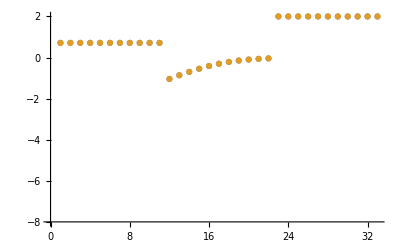

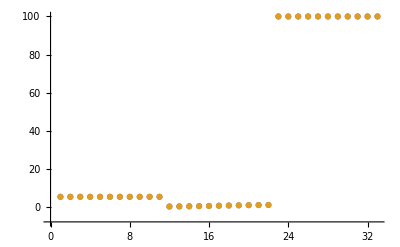

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

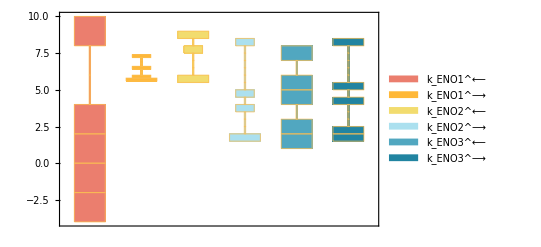

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

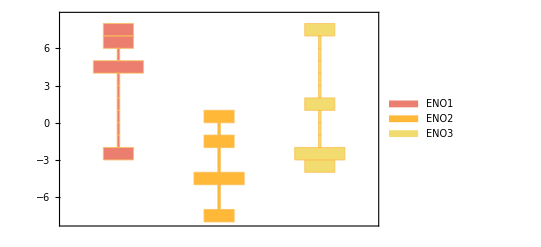

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

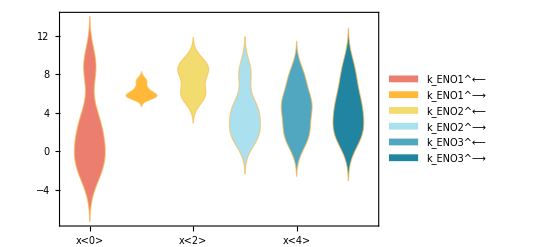

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

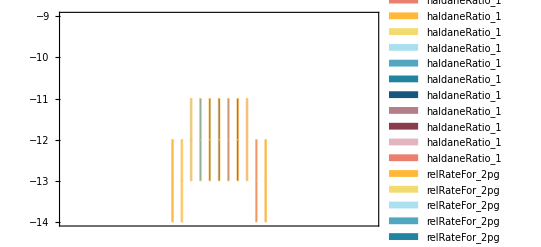

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.0001 | 0.0001 | 2.25148×10^-10

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
100 | 100. | 2.92118×10^-10

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

data value | predicted value | error in %
{}⟦1⟧⟦3⟧ | 1 | (100 Abs[-1+{}⟦1⟧⟦3⟧])/({}⟦1⟧⟦3⟧)

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
5.19 | 5.19 | 3.551×10^-10